# HoRNS - Hawking Radiation of Nonrelativistic Scalars

by Haoran Cui, Yuhsin Tsai, and Tao Xu, based on the work  “Hawking radiation of nonrelativistic scalars: applications to pion and axion production”, arXiv link, Jun 2024.
written for Mathematica 13.1
For questions and comments, please contact [cui00159@umn.edu, ytsai3@nd.edu, tao.xu@ou.edu]

## Initialization

```mathematica
(*In this code, we use the unit where hbar=c=Subscript[k, B]=1.*)
```

### Conversion

The following conversions are designed to simplify the expression in the code and contains various numerical factors like 8π, 2,10^-3, etc., implicitly.

```mathematica
MeVtoInverseMeter=5.3370336766825*^12;(* (hbar×c)^-1, MeV^-1 m^-1*)
MPBHtoMeter=1.4852365918821218*^-30;(* horizon radius Subscript[r, s]=2G×MPBH, g^-1 m*)
MPBHTemperatureConversion=1.0039094730806098*^16;(* black hole temperature T=(8πG)^-1×MPBH^-1, g MeV*)
```

### Radiation Rate

#### Calculate the whole spectrum

```mathematica
CalculateSpectrum[MParticle_,MPBH_]:=
Module[{sb,dt,nl,w,y},
(*we shift all parameters to dimensionless ones: MParticle->Subscript[r, s] MParticle, effective potential V->Subscript[r, s]^2 V, radius r->r/Subscript[r, s]*)
f[r_]:=(1-1/r) (*redshift function, from Eq.(2.4) of the paper*);
V[r_,l_]:=f[r]*(rsm^2+(l(l+1))/r^2+1/r*f'[r]) (*effective potential, from Eq.(2.7) of the paper*);
rs=MPBH*MPBHtoMeter (*Black hole radius, m*);
rsm=rs*(MParticle*MeVtoInverseMeter)(*Subscript[r, s] m in the paper*);
lmin=0(*angular momentum of the modes, we simulate from 0 to 4*);
lmax=4;
lstep=1;
wmin=Max[1.001*rsm,0.001](*energy of the modes. The energy ω is converted to the dimensionless unit Subscript[r, s] ω:=w. Numerically w=Subscript[r, s]*ω*MeVtoInverseLength. In the example setting with MPBH=10^14.5 g, wmin=1.001*rsm=0.339 means the simulation starts from 135 MeV*);
wmax=2(*the simulation ends at 798MeV when MPBH=10^14.5 g*);
wstep=0.001 (*the simulation step is 0.4 MeV when MPBH=10^14.5 g*);
crosecltable={};
radiationrateltable={};
For[l=lmin,l≤lmax,l+=lstep,
For[w=wmin,w≤wmax,w+=wstep,
sb=NDSolve[{(f[r]^2 y''[r] +f[r]*f'[r]*y'[r]+(w^2-V[r,l])*y[r])==0,y[1.001]==1,y'[1.001]==-I*w*1/f[1.001]},y,{r,1.001,2*10^3},(*y is the radial function R, from Eq.(2.6) of the paper. The integration runs from the horizon Subscript[r, s] (practially 1.001*rs) to 2000×Subscript[r, s]. Two boudanry conditions: the function and its derivative are defined as Eq.(2.8) of the paper.*)
Method->{"StiffnessSwitching","BoundaryValues"->{"Shooting","StartingInitialConditions"->{y[1.001]==1,y'[1.001]==-I*w*1/f[1.001]}}},AccuracyGoal->Infinity];
dt=Flatten[Table[y[r]/.sb,{r,1975,2*1000}]];(*when r is larger than 1000*rs, the radial function approaches to its asymptotic form of r -> infity well, so taking the last 25 values of the radial function to fit the second line of the ansatz Eq. (2.8) of the paper*)
nl=NonlinearModelFit[dt,A N[Exp[I *Sqrt[w^2-rsm^2]*x],20]+B N[Exp[-I*Sqrt[w^2-rsm^2]*x],20],{A,B},x];nl["BestFitParameters"];
(*the ratio of the outgoing coefficients A to the ingoing B is reflection amplitude R. Denote |R|^2 as rfl, and the transition rate |T|^2 as 1-rfl*)
tfl=(1-(Abs[A/.nl["BestFitParameters"]]/Abs[B/.nl["BestFitParameters"]])^2) ;(*Transition Rate for different angular momentum l*)
crosecl=Pi/(w^2-rsm^2)* (2 l+1)*(tfl) /(4 Pi*(27/16));(*cross section for different angular momentum l*)
radiationratel=1/(2π) 1/(Exp[4 Pi*w]-1) (2 l+1)*(tfl) ;(*radiation rate for different angular momentum l. In the unit of w, the exponential factor ω/BHTemperature=4π w.*)
crosecltable=Append[crosecltable,crosecl];
radiationrateltable=Append[radiationrateltable,radiationratel];];
];
crosecltable;
radiationrateltable;
scaledcrosec=Plus @@ Partition[crosecltable,Length[crosecltable]/(lmax-lmin+1)];(*sum over the contributions from different angular momenta*)
radiationrate=Plus @@ Partition[radiationrateltable,Length[radiationrateltable]/(lmax-lmin+1)];(*sum over the contributions from different angular momenta*)
totalcrosecNR=Interpolation[Table[{wmin+(i-1)*wstep,scaledcrosec[[i]]},{i,1,Length[scaledcrosec]}]];(*rescale the unit of x-axis to Subscript[r, s] ω. The final function for the cross section*)
dNdEdtNR=Interpolation[Table[{wmin+(i-1)*wstep,radiationrate[[i]]},{i,1,Length[radiationrate]}]]; (*rescale the unit of x-axis to Subscript[r, s] ω. The final function for the radiation rate*)
]
```

#### Calculate only one single point of the spectrum

```mathematica
CalculateSinglePoint[MParticle_,MPBH_,Escalar_]:=Module[{crosecl,radiationratel,y,tfl,rfl,crosecltable,radiationrateltable},
f[r_]:=(1-1/r) ;
V[r_,l_]:=f[r]*(rsm^2+(l(l+1))/r^2+1/r*f'[r]);
rs=MPBH*MPBHtoMeter ;
rsm=rs*(MParticle*MeVtoInverseMeter);
w=rs*(Escalar*MeVtoInverseMeter);
lmin=0(*angular momentum of the modes, we simulate from 0 to 4*);
lmax=4;
lstep=1;
crosecltable={};
radiationrateltable={};
For[l=lmin,l≤lmax,l+=lstep,
sb=NDSolve[{(f[r]^2 y''[r] +f[r]*f'[r]*y'[r]+(w^2-V[r,l])*y[r])==0,y[1.001]==1,y'[1.001]==-I*w*1/f[1.001]},y,{r,1.001,2*10^3},(*y is the radial function R, from Eq.(2.6) of the paper. The integration runs from the horizon Subscript[r, s] (practially 1.001*rs) to 2000×Subscript[r, s]. Two boudanry conditions: the function and its derivative are defined as Eq.(2.8) of the paper.*)
Method->{"StiffnessSwitching","BoundaryValues"->{"Shooting","StartingInitialConditions"->{y[1.001]==1,y'[1.001]==-I*w*1/f[1.001]}}},AccuracyGoal->Infinity];
dt=Flatten[Table[y[r]/.sb,{r,1975,2*1000}]];(*when r is larger than 1000*rs, the radial function approaches to its asymptotic form of r -> infity well, so taking the last 25 values of the radial function to fit the second line of the ansatz Eq. (2.8) of the paper*)
nl=NonlinearModelFit[dt,A N[Exp[I *Sqrt[w^2-rsm^2]*x],20]+B N[Exp[-I*Sqrt[w^2-rsm^2]*x],20],{A,B},x];nl["BestFitParameters"];
(*the ratio of the outgoing coefficients A to the ingoing B is reflection amplitude R. Denote |R|^2 as rfl, and the transition rate |T|^2 as 1-rfl*)
tfl=(1-(Abs[A/.nl["BestFitParameters"]]/Abs[B/.nl["BestFitParameters"]])^2) ;(*Transition Rate for different angular momentum l*)
crosecl=Pi/(w^2-rsm^2)* (2 l+1)*(tfl) /(4 Pi*(27/16))*HeavisideTheta[w-rsm];
radiationratel=1/(2π) 1/(Exp[4 Pi*w]-1) (2 l+1)*(tfl)*HeavisideTheta[w-rsm];
crosecltable=Append[crosecltable,crosecl];
radiationrateltable=Append[radiationrateltable,radiationratel];];
scaledcrosec=Total [crosecltable];
radiationrate=Total[radiationrateltable];
If[w>rsm,
Print["When the energy ω of the scalar particle = ",Escalar," MeV (r_sω = ", w, "), the cross section σ/(27  π SuperscriptBox[G, 2] SuperscriptBox[MPBH, 2]) = ",scaledcrosec, " and the radiation rate dN_scalar/dtdω = ",radiationrate, " MeV^-1 s^-1 with the angular momentum from 0 to 4 summed over."],
Print["The energy ω of the scalar particle is ", Escalar, " MeV < its mass ", MParticle, " MeV, and cannot be detected at infinity since it is not on-shell. "]
]
]
```

## How to use the code

### Define parameters

Here are the reference values that the paper uses. MParticle=134.98 MeV is the mass of neutral pion π^0.

```mathematica
MPBH=10^14.5(*Black hole mass, g*);
MParticle=134.98(*Particle mass, MeV*);
```

Here  is the black hole temperature in MeV for reference.

```mathematica
Print["When the black hole mass M = ",MPBH," g, the Hawking temperature T = ", MPBH^-1*MPBHTemperatureConversion " MeV."]
```

When the black hole mass M = 3.16228×10^14 g, the Hawking temperature T = 31.7464  MeV.

### Run the spectrum calculation code

The CalculateSpectrum function takes some time to finish.

```mathematica
CalculateSpectrum[MParticle,MPBH](*It generates the interpolated functions of the total cross section, totalcrosecNR, and the total radiation rate, dNdEdtNR, of the scalar particle. The contributions of orbital angular momenta from 0 to 4 are summed over. The number of angular momenta modes can be adjusted in the "Radiation Rate" section by changing lmin and lmax.*)
```

$Aborted

### Example 1: Hawking radiation rate at a specific energy of the emitted particle

If only need the radiation rate at a specific energy, please run the following:

```mathematica
CalculateSinglePoint[MParticle,MPBH,10(*emitted particle energy, MeV. Note the divergent cross section at the particle energy = MParticle point may lead to a numerical error warning message.*)]
```

The energy ω of the scalar particle is 10 MeV < its mass 134.98 MeV, and cannot be detected at infinity since it is not on-shell.

### Example 2: Hawking radiation spectrum of the emitted particle [the dark blue solid line of Fig. 4 of the paper, based upon the Eq. (2.11).]

To avoid overfitting, the piecewise function is introduced to cut the production rate at energy ω =  mass m since only on-shell particles can be detected at infinity.

```mathematica
CutdNdEdtNR[rsEscalar_]:=Piecewise[{{dNdEdtNR[rsEscalar],rsEscalar>rsm(*Subscript[r, s] m*)},{10^-50(*a very small value to avoid Log[0] in the following log-plot*),rsEscalar<=rsm}}]
```

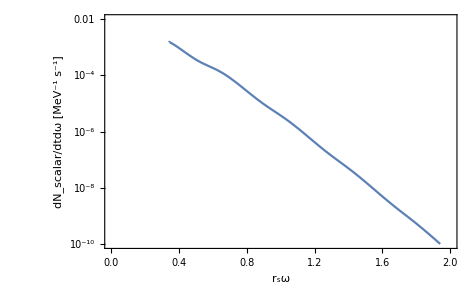

```mathematica
LogPlot[CutdNdEdtNR[rsEscalar],{rsEscalar,0,2(*the span of energy can be adjusted in the "Radiation Rate" section by changing wmin and wmax*)},Frame->True,FrameLabel->{"r_sω","dN_scalar/dtdω [MeV^-1 s^-1]"},PlotRange->{10^-10,10^-2}]//Quiet
```

```mathematica
(*The normalized dimensionless unit Subscript[r, s] ω is used for the x-axis. In the current parameter setting with MPBH=10^14.5 g, Subscript[r, s]=1/398 MeV^-1, so one can convert the unit Subscript[r, s] ω back to ω as the following*)
```

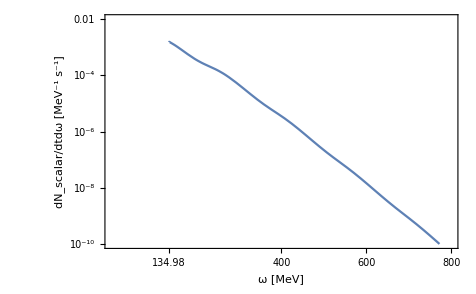

```mathematica
LogPlot[CutdNdEdtNR[Escalar*1/398],{Escalar,0,800},Frame->True, FrameLabel->{"ω [MeV]","dN_scalar/dtdω [MeV^-1 s^-1]"},FrameTicks->{{Automatic,None},{{134.98,400,600,800},None}},PlotRange->{10^-10,10^-2}]//Quiet
```

### Example 3: Cross section [the dark blue solid line of Fig. 3 of the paper, based upon the Eq. (2.10).]

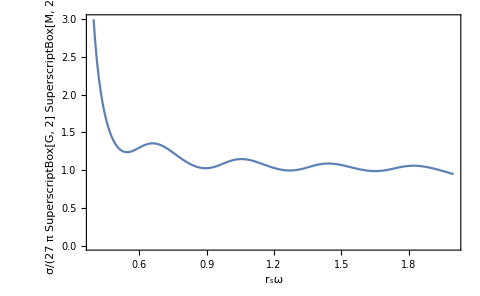

```mathematica
Plot[totalcrosecNR[rsEscalar],{rsEscalar,0,2},Frame->True,FrameLabel->{"r_sω","σ/(27  π SuperscriptBox[G, 2] SuperscriptBox[M, 2])"},PlotRange->{All,{0,3}}]//Quiet
```